# Sum of Lagrange numbers

```mathematica
SetDirectory[NotebookDirectory[]];
markovNums = ReadList["Markov10000.txt"];
S = 4-GoldenRatio-√2;
c=0.18071710471180647805779264904916762147630562767088273^(-.5);
markovNums[[1000]]
```

60362212372938768121282741975801

```mathematica
sumTo[n_]:=Sum[3-√(9-4/markovNums[[j]]^2),{j,1,n}];
R[n_] := S - sumTo[n];
RLog[n_] := Log[R[n]];
RLog10[n_] := Log10[R[n]];
expectedR[n_] := (6 √n)/c ⅇ^(-2c √n);
expectedRLog[n_] := -2c √n+Log[n]/2+Log[6/c];
expectedRLog10[n_] := (-2c √n)/Log[10]+Log10[n]/2+Log10[6/c];
RLin[n_]:= -RLog[n]+Log[n]/2+Log[6/c];
expectedRLin[n_] := 2c √n;
Exp[N[RLog[2000],10]]
```

Indeterminate

```mathematica
tableexpectedRLog2 = Table[expectedRLog[n],{n,1,100}];
tableRLog2 = Table[N[RLog[n],10],{n,1,100}];
tableexpectedRLog3 = Table[expectedRLog[n],{n,1,1000}];
tableRLog3 = Table[N[RLog[n],10],{n,1,1000}];
```

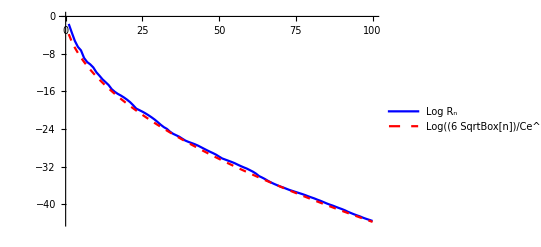

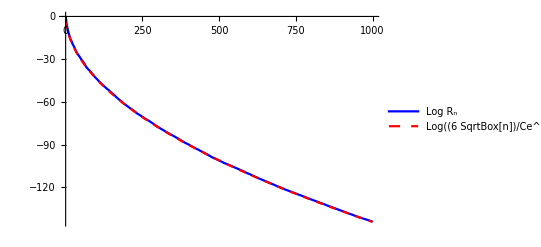

```mathematica
ListLinePlot[{tableRLog2,tableexpectedRLog2},PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"Log R_n","Log((6 SqrtBox[n])/Ce^(-2 C SqrtBox[n]))"}]
ListLinePlot[{tableRLog3,tableexpectedRLog3},PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"Log R_n","Log((6 SqrtBox[n])/Ce^(-2 C SqrtBox[n]))"}]
```

```mathematica
tableexpectedR2 = Table[N[expectedR[n],10],{n,1,100}];
tableR2 = Table[Exp[N[RLog[n],10]],{n,1,100}];
tableexpectedR3 = Table[N[expectedR[n],10],{n,1,1000}];
tableR3 = Table[Exp[N[RLog[n],10]],{n,1,1000}];
```

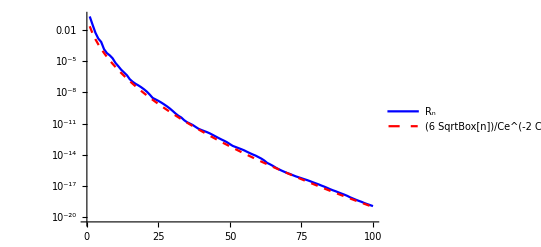

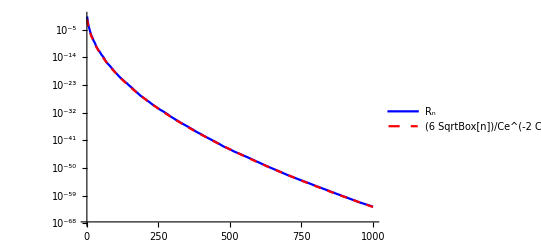

```mathematica
ListLogPlot[{tableR2,tableexpectedR2},Joined->True,PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"R_n","(6 SqrtBox[n])/Ce^(-2 C SqrtBox[n])"}]
ListLogPlot[{tableR3,tableexpectedR3},Joined->True,PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"R_n","(6 SqrtBox[n])/Ce^(-2 C SqrtBox[n])"}]
```

```mathematica
tableexpectedRLin2 = Table[expectedRLin[n],{n,1,100}];
tableRLin2 = Table[N[RLin[n],10],{n,1,100}];
tableexpectedRLin3 = Table[expectedRLin[n],{n,1,1000}];
tableRLin3 = Table[N[RLin[n],10],{n,1,1000}];
```

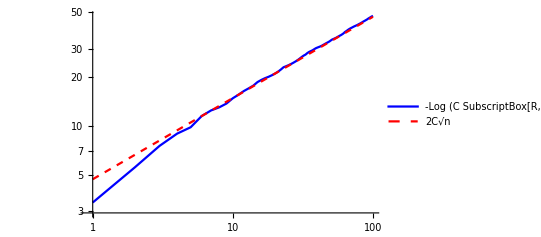

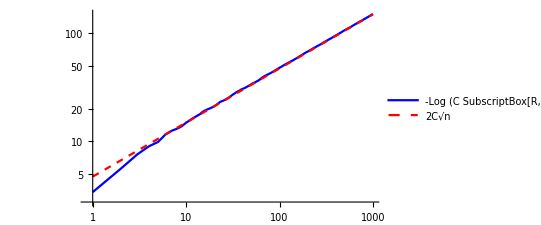

```mathematica
ListLogLogPlot[{tableRLin2,tableexpectedRLin2},Joined->True,PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"-Log (C SubscriptBox[R, n])/(6 SqrtBox[n])","2C√n"},AxesOrigin->{0,0},AspectRatio->Automatic, Ticks->{{2,10,100},{10.0, 20.0, 50.0}}]
ListLogLogPlot[{tableRLin3,tableexpectedRLin3},Joined->True,PlotStyle->{{Joined,Blue},{Dashed,Red}},PlotLegends->{"-Log (C SubscriptBox[R, n])/(6 SqrtBox[n])","2C√n"},AxesOrigin->{0,0}, AspectRatio->Automatic, Ticks->{{2,10,100, 1000},{10.0, 100.0}}]
```